## Conformal blocks

### Definition

```mathematica
S[h1_,h2_,h3_,h4_,h_][w_]:=Gamma[2h]/(Gamma[h+h2-h1]Gamma[h+h4-h3]Gamma[2h1])w^(2h1-1)Hypergeometric2F1[h+h1-h2,1-h+h1-h2,2h1,w]
```

```mathematica
T[h1_,h2_,h3_,h4_,h_][w_]:=1/(Gamma[h+h1-h3]Gamma[h2+h4-h])w^(h+h1-h3-1)Hypergeometric2F1[h-h2-h4+1,h+h4-h2,2h,w]
```

### Identical operators

```mathematica
S[hϕ_,h_][w_]:=Gamma[2h]/(Gamma[h]^2 Gamma[2hϕ])w^(2hϕ-1)Hypergeometric2F1[h,1-h,2hϕ,w]

S[hϕ,h][w]==S[hϕ,hϕ,hϕ,hϕ,h][w]
```

True

```mathematica
T[hϕ_,h_][w_]:=1/(Gamma[h]Gamma[2hϕ-h])w^(h-1)Hypergeometric2F1[h,h-2hϕ+1,2h,w]

T[hϕ,h][w]==T[hϕ,hϕ,hϕ,hϕ,h][w]//FullSimplify
```

True

### Normalization

```mathematica
Sx[hϕ_,h_][w_]:=1/Gamma[2hϕ] w^(2hϕ-1)Hypergeometric2F1[h,1-h,2hϕ,w]

S[hϕ,h][w]==Gamma[2h]/Gamma[h]^2 Sx[hϕ,h][w]
```

True

```mathematica
Tx[hϕ_,h_][w_]:=Sin[π(2hϕ-h)]/π(Gamma[h]Gamma[h-2hϕ+1])/Gamma[2h] w^(h-1)Hypergeometric2F1[h,h-2hϕ+1,2h,w]

T[hϕ,h][w]==Gamma[2h]/Gamma[h]^2 Tx[hϕ,h][w]//FullSimplify
```

True

### h=1+h_1-h_2+n

When h=1+h_1-h_2+n, the s-channel block is a Jacobi polynomial:

```mathematica
S[h1,h2,h3,h4,h][w]==Gamma[2h]/(Gamma[h+h1+h2-1]Gamma[h+h4-h3])w^(2h1-1)JacobiP[n,2h1-1,1-2h2,1-2w]/.{h->1+h1-h2+n}//FullSimplify
```

True

We can then make use of the orthogonality of Jacobi polynomials:

```mathematica
(*Table[((Gamma[2h1+n]Gamma[2-2h2+n])/((2h1-2h2+2n+1)Gamma[2h1-2h2+n+1]n!))^-1 Integrate[w^(2h1-1)(1-w)^(1-2h2)JacobiP[j,2h1-1,1-2h2,1-2w]JacobiP[n,2h1-1,1-2h2,1-2w],{w,0,1},Assumptions->h1>0&&h2<1],{j,0,3},{n,0,3}]//FullSimplify//MatrixForm*)
```

This becomes:

```mathematica
(*Table[Integrate[(Pochhammer[2-2h,n]/Gamma[h+h4-h3])^-1(1-w)^(1-2h2)((-1)^j j!)/Gamma[2-2h2+j] JacobiP[j,2h1-1,1-2h2,1-2w]S[h1,h2,h3,h4,h][w]/.{h->1+h1-h2+n},{w,0,1},Assumptions->h1>0&&h2<1/2],{j,0,3},{n,0,3}]//FullSimplify//MatrixForm*)
```

For generic h, we have:

```mathematica
Stilde[h1_,h2_,h3_,h4_,h_,j_]:=Gamma[2h]/(Gamma[h+h2-h1]Gamma[h+h4-h3])1/(Gamma[h+h1-h2]Gamma[1-h+h1-h2])1/((h+h1-h2+j)(1-h+h1-h2+j))
```

```mathematica
Table[Module[{h1,h2,h3,h4,h},
h1=RandomReal[{1/2,1}];
h2=RandomReal[{0,1/2}];
{h3,h4,h}=RandomReal[{0,1},3];
((-1)^j j!)/Gamma[2-2h2+j] NIntegrate[(1-w)^(1-2h2)JacobiP[j,2h1-1,1-2h2,1-2w]S[h1,h2,h3,h4,h][w],{w,0,1}]/Stilde[h1,h2,h3,h4,h,j]
],{5},{j,0,4}]
```

{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}}

The t-channel block is instead

```mathematica
Ttilde[h1_,h2_,h3_,h4_,h_,j_]:=Gamma[2h]/(Gamma[h+h1-h3]Gamma[h+h4-h2])Sin[π(h2+h4-h)]/π(Gamma[h+h1-h3]Gamma[h+h4-h2]Gamma[h-h1-h3+1]Gamma[h-h2-h4+1])/(Gamma[2h]Gamma[h+h1-2h2-h3+2+j]Gamma[h-h1-h3+1-j])HypergeometricPFQ[{h+h1-h3,h+h4-h2,h-h1-h3+1,h-h2-h4+1},{2h,h+h1-2h2-h3+2+j,h-h1-h3+1-j},1]
```

```mathematica
Table[Module[{h1,h2,h3,h4,h},
h1=RandomReal[{1/2,1}];
h2=RandomReal[{0,1/2}];
{h3,h4,h}=RandomReal[{0,1},3];
((-1)^j j!)/Gamma[2-2h2+j] NIntegrate[(1-w)^(1-2h2)JacobiP[j,2h1-1,1-2h2,1-2w]T[h1,h2,h3,h4,h][w],{w,0,1}]/Ttilde[h1,h2,h3,h4,h,j]
],{5},{j,0,4}]
```

{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}}

The relation can be inverted to get S_h(w) and T_h(w) as infinite sums of Jacobi polynomials

```mathematica
Table[Module[{h1,h2,h3,h4,h,w},
h1=RandomReal[{1/2,1}];
h2=RandomReal[{0,1/2}];
{h3,h4,h,w}=RandomReal[{0,1},4];
S[h1,h2,h3,h4,h][w]/(w^(2h1-1)∑_(j=0)^50 ((-1)^j(2h1-2h2+2j+1)Gamma[2h1-2h2+j+1])/Gamma[2h1+j] Stilde[h1,h2,h3,h4,h,j]JacobiP[j,2h1-1,1-2h2,1-2w])
],{20}]
```

{0.99431,1.01154,1.00382,0.999539,1.00447,0.974868,0.995729,1.00465,1.01253,1.00442,0.833461,1.13635,1.00894,1.02377,1.02701,0.987427,1.18179,0.99865,0.993061,0.997308}

With identical operators, this is:

```mathematica
Stilde[hϕ_,h_,j_]:=Gamma[2h]/Gamma[h]^2 Sin[π h]/π 1/((h+j)(1-h+j))

Stilde[hϕ,hϕ,hϕ,hϕ,h,j]==Stilde[hϕ,h,j]//FullSimplify
```

True

```mathematica
Ttilde[hϕ_,h_,j_]:=Gamma[2h]/Gamma[h]^2 Sin[π(2hϕ-h)]/π(Gamma[h]^2 Gamma[h-2hϕ+1]^2)/(Gamma[2h]Gamma[h-2hϕ+2+j]Gamma[h-2hϕ+1-j])HypergeometricPFQ[{h,h,h-2hϕ+1,h-2hϕ+1},{2h,h-2hϕ+2+j,h-2hϕ+1-j},1]

Ttilde[hϕ,hϕ,hϕ,hϕ,h,j]==Ttilde[hϕ,h,j]//FullSimplify
```

True

(S̃)_(h,j) and (T̃)_(h,j) can also be obtained from the Euclidean blocks:

```mathematica
fp[hϕ_,h_][x_]:=Gamma[2h]/Gamma[h]^2(1-x)^(2hϕ)Hypergeometric2F1[h,1-h,1,x]
fm[hϕ_,h_][x_]:=Sin[π(2hϕ-h)]/π x^(h-2hϕ)(1-x)^(2hϕ)Hypergeometric2F1[h,h,2h,x]
```

```mathematica
Table[Module[{hϕ,h},
{hϕ,h}=RandomReal[{0,1},2];
(-1)^j NIntegrate[(1-x)^(-2hϕ)LegendreP[j,1-2x]fp[hϕ,h][x],{x,0,1}]/Stilde[hϕ,h,j]],
{j,0,5},{5}]
```

{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}}

```mathematica
Table[Module[{hϕ,h},
hϕ=RandomReal[{0,1/2}];
h=RandomReal[{1,2}];
(-1)^j NIntegrate[(1-x)^(-2hϕ)LegendreP[j,1-2x]fm[hϕ,h][x],{x,0,1}]/Ttilde[hϕ,h,j]],
{j,0,5},{5}]
```

{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}}

### h=h_1+h_2+n

When h=h_1+h_2+n, the s-channel block is again a Jacobi polynomial:

```mathematica
S[h1,h2,h3,h4,h][w]==(Gamma[2h]Gamma[h-h1-h2+1])/(Gamma[h+h1-h2]Gamma[h+h2-h1]Gamma[h+h4-h3])w^(2h1-1)(1-w)^(2h2-1)JacobiP[n,2h1-1,2h2-1,1-2w]/.{h->h1+h2+n}//FullSimplify
```

True

```mathematica
S[h1,h2,h3,h4,h][w]==(n!Gamma[2h])/(Gamma[h+h1-h2]Gamma[h+h2-h1]Gamma[h+h4-h3])w^(2h1-1)(1-w)^(2h2-1)JacobiP[n,2h1-1,2h2-1,1-2w]/.{h->h1+h2+n}//FullSimplify
```

True

We can then make use of the orthogonality of Jacobi polynomials:

```mathematica
(*Table[((Gamma[2h1+n]Gamma[2h2+n])/((2h1+2h2+2n-1)Gamma[2h1+2h2+n-1]n!))^-1 Integrate[w^(2h1-1)(1-w)^(2h2-1)JacobiP[j,2h1-1,2h2-1,1-2w]JacobiP[n,2h1-1,2h2-1,1-2w],{w,0,1},Assumptions->h1>0&&h2>0],{j,0,3},{n,0,3}]//FullSimplify//MatrixForm*)
```

This becomes:

```mathematica
(*Table[Integrate[((n!Pochhammer[2-2h,n])/(Gamma[h+h2-h1]Gamma[h+h4-h3]))^-1((-1)^j j!)/Gamma[2h2+j] JacobiP[j,2h1-1,2h2-1,1-2w]S[h1,h2,h3,h4,h][w]/.{h->h1+h2+n},{w,0,1},Assumptions->h1>0&&h2>0],{j,0,3},{n,0,3}]//FullSimplify//MatrixForm*)
```

For generic h, we have:

```mathematica
S[h1_,h2_,h3_,h4_,h_,j_]:=Gamma[2h]/(Gamma[h+h2-h1]Gamma[h+h4-h3])1/(Gamma[h1+h2+h-1]Gamma[h1+h2-h])1/((h1+h2-h+j)(h1+h2+h-1+j))
```

```mathematica
Table[Module[{h1,h2,h3,h4,h},
{h1,h2,h3,h4}=RandomReal[{1/2,2},4];
h=RandomReal[{4,10}];
((-1)^j j!)/Gamma[2h2+j] NIntegrate[JacobiP[j,2h1-1,2h2-1,1-2w]S[h1,h2,h3,h4,h][w],{w,0,1}]/S[h1,h2,h3,h4,h,j]
],{5},{j,0,4}]
```

{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}}

The t-channel block is instead

```mathematica
T[h1_,h2_,h3_,h4_,h_,j_]:=Gamma[h-h1-h3+1]/(Gamma[h2+h4-h]Gamma[h+h1+2h2-h3+j]Gamma[h-h1-h3+1-j])HypergeometricPFQ[{h+h2+h4-1,h+h2-h4,h+h1-h3,h-h1-h3+1},{2h,h+h1+2h2-h3+j,h-h1-h3+1-j},1]
```

```mathematica
Table[Module[{h1,h2,h3,h4,h},
{h1,h2,h3,h4}=RandomReal[{1/2,2},4];
h=RandomReal[{4,10}];
((-1)^j j!)/Gamma[2h2+j] NIntegrate[JacobiP[j,2h1-1,2h2-1,1-2w]T[h1,h2,h3,h4,h][w],{w,0,1}]/T[h1,h2,h3,h4,h,j]
],{5},{j,0,4}]
```

{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}}

The relation can be inverted to get S_h(w) and T_h(w) as infinite sums of Jacobi polynomials:

```mathematica
Table[Module[{h1,h2,h3,h4,h,w},
{h1,h2,h3,h4}=RandomReal[{1/2,2},4];
h=RandomReal[{4,10}];
w=RandomReal[{0,1}];
S[h1,h2,h3,h4,h][w]/(w^(2h1-1)(1-w)^(2h2-1)∑_(j=0)^100 ((-1)^j(2h1+2h2+2j-1)Gamma[2h1+2h2+j-1])/Gamma[2h1+j] S[h1,h2,h3,h4,h,j]JacobiP[j,2h1-1,2h2-1,1-2w])
],{20}]
```

{1.13781,0.619459,0.549327,1.0002,0.954501,0.702405,0.989571,0.85937,0.997588,0.861344,1.00001,0.988338,0.999304,1.44191,0.571317,-0.106077,0.63308,0.318564,0.30269,-45.7771}

With identical operators, this is:

```mathematica
S[hϕ_,h_,j_]:=Gamma[2h]/Gamma[h]^2 1/(Gamma[2hϕ+h-1]Gamma[2hϕ-h])1/((2hϕ-h+j)(2hϕ+h-1+j))

S[hϕ,hϕ,hϕ,hϕ,h,j]==S[hϕ,h,j]//FullSimplify
```

True

```mathematica
S[hϕ,h,j]-Gamma[2h-1]/Gamma[h]^2 1/(Gamma[2hϕ+h-1]Gamma[2hϕ-h])(1/(2hϕ-h+j)-1/(2hϕ+h-1+j))//FullSimplify
```

0

```mathematica
T[hϕ_,h_,j_]:=Gamma[h-2hϕ+1]/(Gamma[2hϕ-h]Gamma[h-2hϕ+1-j]Gamma[h+2hϕ+j])HypergeometricPFQ[{h,h,h+2hϕ-1,h-2hϕ+1},{2h,h+2hϕ+j,h-2hϕ+1-j},1]

T[hϕ,hϕ,hϕ,hϕ,h,j]==T[hϕ,h,j]//FullSimplify
```

True

```mathematica
T[hϕ,h,j]==Gamma[2h]/Gamma[h]^2 1/(Gamma[2hϕ-h]Gamma[h+2hϕ-1])(Gamma[h]^2 Gamma[h+2hϕ-1]Gamma[h-2hϕ+1])/(Gamma[2h]Gamma[h-2hϕ+1-j]Gamma[h+2hϕ+j])HypergeometricPFQ[{h,h,h+2hϕ-1,h-2hϕ+1},{2h,h+2hϕ+j,h-2hϕ+1-j},1]//FullSimplify
```

True

### Identity operator h=0

```mathematica
Limit[S[h1,h1,h4,h4,h,j],h->0]
```

0

```mathematica
S0[h1_,h4_,j_]:=0
```

```mathematica
T[h1,h2,h1,h2,h,j]==Gamma[h-2h1+1]/(Gamma[2h2-h]Gamma[h+2h2+j]Gamma[h-2h1+1-j])HypergeometricPFQ[{h+2h2-1,h,h,h-2h1+1},{2h,h+2h2+j,h-2h1+1-j},1]
```

True

```mathematica
T[h1,h2,h1,h2,h,j]==1/Gamma[2h2-h] Gamma[h-2h1+1]/(Gamma[h+2h2+j]Gamma[h-2h1+1-j])+Gamma[2h]/Gamma[h]^2 1/(Gamma[2h2-h]Gamma[h+2h2-1])∑_(k=1)^∞ (Gamma[h+k]^2 Gamma[h+2h2-1+k]Gamma[h-2h1+1+k])/(k!Gamma[2h+k]Gamma[h+2h2+j+k]Gamma[h-2h1+1-j+k])//FullSimplify
```

True

```mathematica
T0[h1_,h2_,j_]:=(-1)^j/Gamma[2h2]^2 Pochhammer[2h1,j]/Pochhammer[2h2,j]
```

```mathematica
Table[T0[h1,h2,j]-1/Gamma[2h2-h] Gamma[h-2h1+1]/(Gamma[h+2h2+j]Gamma[h-2h1+1-j])/.{h->0},{j,0,5}]//FullSimplify
```

{0,0,0,0,0,0}

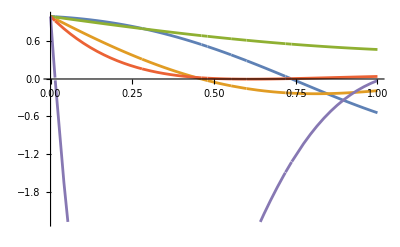

```mathematica
Table[T[h1,h2,h1,h2,h,j]/T0[h1,h2,j]/.{h1->RandomReal[{0,2}],h2->RandomReal[{0,2}]},{j,0,4}];
Plot[%,{h,0,1}]
```

```mathematica
S0[hϕ_,j_]:=S0[hϕ,hϕ,j]
T0[hϕ_,j_]:=T0[hϕ,hϕ,j]
```

```mathematica
T0[hϕ,j]==(-1)^j/Gamma[2hϕ]^2
```

True

### Efficient evaluation

Extract a recurrent prefactor independent of j:

```mathematica
κ[hϕ_,h_]:=Gamma[2h]/Gamma[h]^2 1/(Gamma[2hϕ-h]Gamma[h+2hϕ-1])
```

The rest takes a simpler form:

```mathematica
S[hϕ,h,j]==κ[hϕ,h]/((2hϕ-h+j)(2hϕ+h-1+j))
```

True

```mathematica
Tk[hϕ_,h_,j_,k_]:=(Gamma[h+k]^2 Gamma[h+2hϕ-1+k]Gamma[h-2hϕ+1+k])/(k!Gamma[2h+k]Gamma[h-2hϕ+1-j+k]Gamma[h+2hϕ+j+k])
```

```mathematica
T[hϕ,h,j]==κ[hϕ,h]∑_(k=0)^∞ Tk[hϕ,h,j,k]//FullSimplify
```

True

The terms in the sum decrease like k^-2, so the series is absolutely convergent:

```mathematica
Limit[Tk[hϕ,h,j,k]/(1/k^2),k->∞]
```

1

There is a simple recurrence relation in j for the k-th term in the sum:

```mathematica
Tk[hϕ,h,j+1,k]==(h-2hϕ-j+k)/(h+2hϕ+j+k)Tk[hϕ,h,j,k]//FullSimplify
```

True

```mathematica
Series[Tk[hϕ,h,j+1,k]/Tk[hϕ,h,j,k]//FullSimplify,{j,∞,1}]
```

-1+(2 (h+k))/j+O[1/j]^2

```mathematica
Tk[hϕ,h,0,k]==Gamma[h+k]^2/(k!Gamma[2h+k](h+2hϕ+k-1))//FullSimplify
```

True

For the term j=0, there is a recursion relation in h:

```mathematica
Tk[hϕ,h+1,0,k]-((h+k)^2(h+2hϕ+k-1))/((2h+k+1)(2h+k)(h+2hϕ+k))Tk[hϕ,h,0,k]//FullSimplify
```

0

```mathematica
Series[Tk[hϕ,h+1,0,k]/Tk[hϕ,h,0,k]//FullSimplify,{h,∞,0}]
```

1/4+O[1/h]^1

Note that the initial contribution decrease as k^-2, so the sum over k is absolutely convergent:

```mathematica
Limit[Tk[hϕ,h,0,k]/(1/k^2),k->∞]
```

1

When h is an integer, with the recursion starting at h=1, this can be written without Γ function:

```mathematica
Tk[hϕ,1,0,k]==1/((k+1)(2hϕ+k))//FullSimplify
```

True

Note that the recursion relation in h can also be expressed with increment 2:

```mathematica
Tk[hϕ,h+2,0,k]-((h+k)^2(h+k+1)^2(h+2hϕ+k-1))/((2h+k+3)(2h+k+2)(2h+k+1)(2h+k)(h+2hϕ+k+1))Tk[hϕ,h,0,k]//FullSimplify
```

0

This is relevant with h taking double-twist dimension, starting at h=2 h_ϕ or h=2 h_ϕ+1:

```mathematica
Tk[hϕ,2hϕ,0,k]==Gamma[2hϕ+k]^2/(k!Gamma[4hϕ+k](4hϕ+k-1))//FullSimplify
```

True

```mathematica
Tk[hϕ,2hϕ+1,0,k]==Gamma[2hϕ+k+1]^2/(k!Gamma[4hϕ+k+2](4hϕ+k))//FullSimplify
```

True

Finally, the series in k also admits a recursive definition:

```mathematica
Tk[hϕ,h,0,k+1]/Tk[hϕ,h,0,k]-((h+k)^2(h+2hϕ+k-1))/((k+1)(2h+k)(h+2hϕ+k))//FullSimplify
```

0

```mathematica
Series[Tk[hϕ,h,0,k+1]/Tk[hϕ,h,0,k]//FullSimplify,{k,∞,1}]
```

1-2/k+O[1/k]^2

```mathematica
Tk[hϕ,h,0,0]==Gamma[h]^2/(Gamma[2h](h+2hϕ-1))//FullSimplify
```

True

```mathematica
κ[hϕ,h]Tk[hϕ,h,0,0]==1/(Gamma[2hϕ-h]Gamma[2hϕ+h])//FullSimplify
```

True

### Other representations for T

```mathematica
Talt[h1_,h2_,h3_,h4_,h_,j_]:=((-1)^j j!Gamma[2 h]Pochhammer[h1+h3-h,j])/(Gamma[h1-h3+h]Gamma[h2+h4-h]Gamma[h2-h4+h+j+1]Gamma[h2+h4+h+j])∑_(i=0)^j (Pochhammer[h2-h4+h,i]Pochhammer[h2+h4+h-1,i])/(i!Pochhammer[h-h1-h3+1-j,i])HypergeometricPFQ[{j-i+1,h3-h1+h,2 h2+j},{h2-h4+h+j+1,h2+h4+h+j},1]
```

```mathematica
Table[T[h1,h2,h3,h4,h,j]/Talt[h1,h2,h3,h4,h,j]/.{h1->RandomReal[{0,1}],h2->RandomReal[{0,1}],h3->RandomReal[{0,1}],h4->RandomReal[{0,1}],h->RandomReal[{1,2}]},{j,0,10}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Talt2[h1_,h2_,h3_,h4_,h_,j_]:=((-1)^j j!Pochhammer[h1+h3-h,j])/(Gamma[h2+h4-h]Gamma[2 h2+j]Gamma[h1-h3+h+j+1])∑_(i=0)^j (Pochhammer[h1-h3+h,i]Pochhammer[h2-h4+h,i]Pochhammer[h2+h4+h-1,i])/(i!Pochhammer[2h,i]Pochhammer[h-h1-h3+1-j,i])HypergeometricPFQ[{h1-h3+h+i,1-h4-h2+h,h4-h2+h},{h1-h3+h+j+1,2h+i},1]
```

```mathematica
Table[T[h1,h2,h3,h4,h,j]/Talt2[h1,h2,h3,h4,h,j]/.{h1->RandomReal[{0,1}],h2->RandomReal[{0,1}],h3->RandomReal[{0,1}],h4->RandomReal[{0,1}],h->RandomReal[{1,2}]},{j,0,10}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

### Holomorphic external operators

If h_2=0 or h_4=0, the equation is trivial (S_h=T_h=0):

```mathematica
S[h1,0,h3,h4,h1][w]
T[h1,0,h3,h4,h4][w]
```

0

0

```mathematica
S[h1,0,h3,h4,h1,j]
T[h1,0,h3,h4,h4,j]
```

0

0

Same if  h_4=0:

```mathematica
S[h1,h2,h3,0,h3][w]
T[h1,h2,h3,0,h2][w]
```

0

0

```mathematica
S[h1,h2,h3,0,h3,j]
T[h1,h2,h3,0,h2,j]
```

0

0

If h_1=0, the equation is satisfied since S_h=T_h:

```mathematica
Limit[S[ϵ,h2,h3,h4,h2,0],ϵ->0]
T[0,h2,h3,h4,h3,0]
%%==%
```

1/(Gamma[2 h2] Gamma[h2-h3+h4])

1/(Gamma[2 h2] Gamma[h2-h3+h4])

True

```mathematica
Table[Limit[S[ϵ,h2,h3,h4,h2,j],ϵ->0],{j,10}]
Table[T[0,h2,h3,h4,h3,j],{j,10}]
```

{0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0}

Same if h_3=0, the equation is satisfied since S_h=T_h:

```mathematica
S[h1,h2,0,h4,h4,0]//FullSimplify
T[h1,h2,0,h4,h1,0]//FullSimplify
%%==%
```

1/(Gamma[1+h1+h2-h4] Gamma[-h1+h2+h4] Gamma[h1+h2+h4])

1/(Gamma[1+h1+h2-h4] Gamma[-h1+h2+h4] Gamma[h1+h2+h4])

True

```mathematica
Table[S[h1,h2,0,h4,h4,j]==Series[Talt[h1,h2,ϵ,h4,h1,j],{ϵ,0,0}]//Normal//FullSimplify,{j,6}]
```

{True,True,True,True,True,True}

### Asymptotics h→∞

```mathematica
S∞[h1_,h2_,h3_,h4_,h_]:=Sin[π(h-h1-h2)]/(2 π^(3/2))2^(2h)/h^(h1+h2+h3+h4+2(h2-h3)-1/2)
```

```mathematica
S∞ratio[h1,h2,h3,h4,h,j]=1/((h-h1-h2-j) (h1+h2+h-1+j))(Gamma[h]Gamma[h+1/2]Gamma[h-h1-h2+1])/(Gamma[h-h1+h2]  Gamma[h+h1+h2-1] Gamma[h-h3+h4])/(1/h^(h1+h2+h3+h4+2(h2-h3)-1/2));
```

```mathematica
S∞ratio[h1,h2,h3,h4,h,j]==S[h1,h2,h3,h4,h,j]/(S∞[h1,h2,h3,h4,h])//FullSimplify
```

True

```mathematica
Limit[S∞ratio[h1,h2,h3,h4,h,j],h->∞]
```

1

T has the same asymptotics as S, up to a sine:

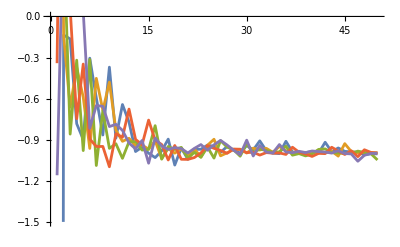

```mathematica
ListLinePlot[Table[Table[Sin[π(h-h1-h2)]/Sin[π(h-h4-h2)] T[h1,h2,h3,h4,h,j]/S[h1,h2,h3,h4,h,j]/.{h1->RandomReal[{0,2}],h2->RandomReal[{0,2}],h3->RandomReal[{0,2}],h4->RandomReal[{0,2}],j->RandomInteger[{0,2}]},{h,1,50}],{5}],PlotRange->{-1.5,0}]
```

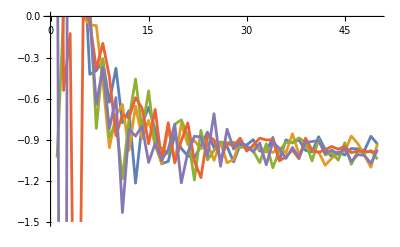

```mathematica
ListLinePlot[Table[Table[Sin[π(h-h1-h2)]/Sin[π(h-h4-h2)] T[h1,h2,h3,h4,h,j]/S[h1,h2,h3,h4,h,j]/.{h1->RandomReal[{0,2}],h2->RandomReal[{2,4}],h3->RandomReal[{0,2}],h4->RandomReal[{0,2}],j->RandomInteger[{0,2}]},{h,1,50}],{5}],PlotRange->{-1.5,0}]
```

### Asymptotics j→∞

Observation: in the case of identical operators, we also have T_(h,j)~S_(h,j) in the limit j->∞, provided that h is sufficiently large:

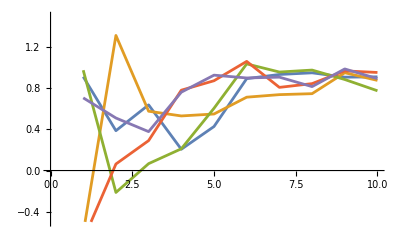

```mathematica
ListLinePlot[Table[Table[T[hϕ,h,j]/S[hϕ,h,j]/.{hϕ->RandomReal[{0,2}],h->RandomInteger[{2,4}]},{j,1,10}],{5}],PlotRange->{-0.5,1.5}]
```

## Crossing equation

### Generalized free field theory

```mathematica
Table[Limit[S[h1,h2,h3,h4,h,j],h->h1+h2+n]-((-1)^j j!Pochhammer[2h1+2h2+j-1,j])/(Gamma[2h2+j]Gamma[h1+h2-h3+h4+j])KroneckerDelta[n,j],{n,0,3},{j,0,3}]//FullSimplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Table[T[h1,h2,h3,h4,h2+h4+n,j],{n,0,5}]
```

{0,0,0,0,0,0}

The case  O_1=O_2, O_3=O_4 is trivial:

```mathematica
S0[h1,h2,j]
Table[T[h1,h1,h2,h2,h1+h2+n,j],{n,0,5}]
```

0

{0,0,0,0,0,0}

The case  O_1=O_3, O_2=O_4 is interesting: it allows to compute the OPE coefficients

```mathematica
SGFF[h1_,h2_,j_]:=((-1)^j j!Pochhammer[2h1+2h2+j-1,j])/Gamma[2h2+j]^2
```

```mathematica
Table[Limit[S[h1,h2,h1,h2,h,j],h->h1+h2+n]-SGFF[h1,h2,j]KroneckerDelta[n,j],{n,0,3},{j,0,3}]//FullSimplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
C2GFF[h1_,h2_,n_]:=(Pochhammer[2 h1,n]Pochhammer[2 h2,n])/(n!Pochhammer[2h1+2h2+n-1,n])
```

```mathematica
T0[h1,h2,n]-C2GFF[h1,h2,n]SGFF[h1,h2,n]//FullSimplify
```

0

```mathematica
C2GFF[h1,h2,h-h1-h2]==(Gamma[h+h1-h2]Gamma[h+h2-h1]Gamma[h1+h2+h-1])/(Gamma[2h1]Gamma[2h2]Gamma[h-h1-h2+1]Gamma[2h-1])//FullSimplify
```

True

```mathematica
C2GFF[hϕ_,n_]:=(2 Pochhammer[2 hϕ,n]^2)/(n!Pochhammer[4hϕ+n-1,n])
```

```mathematica
C2GFF[hϕ,n]==2C2GFF[hϕ,hϕ,n]
```

True

```mathematica
C2GFF[hϕ,h-2hϕ]==(2 Gamma[h]^2 Gamma[2hϕ+h-1])/(Gamma[2hϕ]^2 Gamma[h-2hϕ+1]Gamma[2h-1])//FullSimplify
```

True

```mathematica
C2GFF[1/2,n]==2(n!)^2/((2n)!)//FullSimplify
```

True

### Ising model

```mathematica
hσ=1/16;
hϵ=1/2;
```

```mathematica
ToConformalWeights[OPEcoeffs_]:=Flatten[Map[If[#⟦2⟧==0,{{(#⟦1⟧)/2,(#⟦1⟧)/2,#⟦3⟧}},{{(#⟦1⟧+#⟦2⟧)/2,(#⟦1⟧-#⟦2⟧)/2,#⟦3⟧},{(#⟦1⟧-#⟦2⟧)/2,(#⟦1⟧+#⟦2⟧)/2,#⟦3⟧}}]&,OPEcoeffs],1]
```

```mathematica
cutoff[Λ_,OPEcoeffs_]:=Select[OPEcoeffs,#[[1]]!=0&&#[[2]]!=0&&#[[1]]+#[[2]]<=Λ&]
```

#### ⟨σσσσ⟩

```mathematica
C2σσ=Import["~/repos/QuasiPrimaryData/CFTdata/Ising_ss.csv","Table"]//ToExpression//ToConformalWeights;
Length[C2σσ]
```

2504

```mathematica
cutoff[6,C2σσ]//Length
cutoff[9,C2σσ]//Length
cutoff[12,C2σσ]//Length
```

6

14

27

```mathematica
SSσσσσ[w_,wbar_,Λ_]:=Sum[hhc[[3]]S[hσ,hhc[[1]]][w]S[hσ,hhc[[2]]][wbar],{hhc,cutoff[Λ,C2σσ]}];
```

```mathematica
TTσσσσ[w_,wbar_,Λ_]:=Sum[hhc[[3]]T[hσ,hhc[[1]]][w]T[hσ,hhc[[2]]][wbar],{hhc,cutoff[Λ,C2σσ]}];
```

```mathematica
<<MaTeX`
```

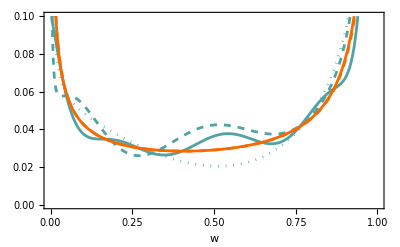

```mathematica
colorS=RGBColor["#51A3A3"];
colorT=RGBColor["#F96900"];
plotσσσσ=Plot[{SSσσσσ[w,1/2,6],SSσσσσ[w,1/2,9],SSσσσσ[w,1/2,12],TTσσσσ[w,1/2,1],TTσσσσ[w,1/2,12]},{w,0,1},PlotStyle->{{colorS,Dotted},{colorS,Dashed},colorS,{colorT,Dashed},colorT},
FrameLabel->"w",Frame->True,PlotRange->{{0,1},{0,0.1}},
BaseStyle->{FontSize->14,FontFamily->"Latin Modern Math"},
PlotLegends->{
Placed[LineLegend[{{colorS,Dotted},{colorS,Dashed},colorS},{MaTeX["\\Lambda = 6"],MaTeX["\\Lambda = 9"],MaTeX["\\Lambda = 12"]},LegendLabel->MaTeX["\\sum_{h + \\bar{h} \\leq \\Lambda} C_{\\sigma\\sigma\\mathcal{O}}^2 S_h(w)S_{\\bar{h}}(\\tfrac{1}{2})"]],After],
Placed[LineLegend[{{colorT,Dashed},colorT},{MaTeX["\\Lambda = 1"],MaTeX["\\Lambda = 12"]},LegendLabel->MaTeX["\\sum_{h + \\bar{h} \\leq \\Lambda} C_{\\sigma\\sigma\\mathcal{O}}^2 T_h(w)T_{\\bar{h}}(\\tfrac{1}{2})"]],After]
}
]
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["Ising_sigma.pdf",plotσσσσ]*)
```

When projected on the orthogonal basis of Jacobi polynomials, however, the OPE does not converge:

```mathematica
j0=0;
j0bar=1;
```

```mathematica
Sσσσσ[h_]=S[hσ,h,j0]//FullSimplify
Sσσσσbar[h_]=S[hσ,h,j0bar]//FullSimplify
```

Gamma[2 h]/(Gamma[9/8-h] Gamma[h]^2 Gamma[1/8+h])

(8 Gamma[2 h])/((9-8 h) (1/8+h) Gamma[1/8-h] Gamma[-7/8+h] Gamma[h]^2)

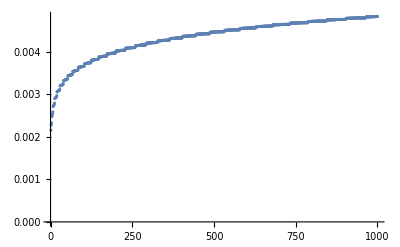

```mathematica
Map[#⟦3⟧Sσσσσ[#⟦1⟧]Sσσσσbar[#⟦2⟧]&,DeleteCases[C2σσ,{___,0,__}][[1;;1000]]]//Accumulate//ListPlot
```

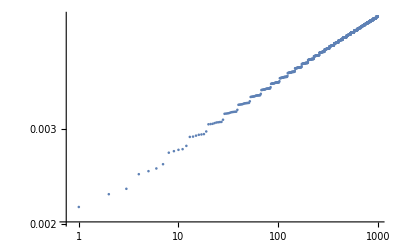

```mathematica
Map[#⟦3⟧Sσσσσ[#⟦1⟧]Sσσσσbar[#⟦2⟧]&,DeleteCases[C2σσ,{___,0,__}][[1;;1000]]]//Accumulate//ListLogLogPlot
```

```mathematica
Tσσσσ[h_]=T[hσ,h,j0]//FullSimplify
Tσσσσbar[h_]=T[hσ,h,j0bar]//FullSimplify
```

(Gamma[2 h] HypergeometricPFQRegularized[{-7/8+h,h,h},{2 h,1/8+h},1])/Gamma[1/8-h]

(Gamma[2 h] Gamma[7/8+h] HypergeometricPFQRegularized[{-7/8+h,h,h,7/8+h},{-1/8+h,2 h,9/8+h},1])/Gamma[1/8-h]

```mathematica
Tσσσσ0=T0[hσ,j0]
Tσσσσ0bar=T0[hσ,j0bar]
```

1/Gamma[1/8]^2

-1/Gamma[1/8]^2

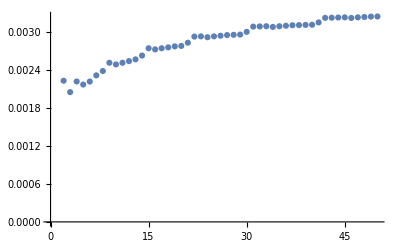

```mathematica
Map[#⟦3⟧If[#⟦1⟧==0,Tσσσσ0,Tσσσσ[#⟦1⟧]]If[#⟦2⟧==0,Tσσσσ0bar,Tσσσσbar[#⟦2⟧]]&,C2σσ[[1;;50]]]//Accumulate//ListPlot
```

#### ⟨σϵσϵ⟩

```mathematica
C2σϵ=Import["~/repos/QuasiPrimaryData/CFTdata/Ising_se.csv","Table"]//ToExpression//ToConformalWeights;
Length[C2σϵ]
```

4473

```mathematica
C2ϵϵ=Import["~/repos/QuasiPrimaryData/CFTdata/Ising_ee.csv","Table"]//ToExpression//ToConformalWeights;
Length[C2ϵϵ]
```

1326

```mathematica
C2σσ1=Import["~/repos/QuasiPrimaryData/CFTdata/Ising_ss1.csv","Table"]//ToExpression//ToConformalWeights;
Length[C2σσ1]
```

1326

```mathematica
C2σσ1[[All,{1,2}]]==C2ϵϵ[[All,{1,2}]]
```

True

```mathematica
CσσCϵϵ={C2ϵϵ[[All,1]],C2ϵϵ[[All,2]],√(C2σσ1⟦All,3⟧*C2ϵϵ⟦All,3⟧)}ᵀ;
```

```mathematica
SSσϵσϵ[w_,wbar_,Λ_]:=Sum[hhc[[3]]S[hσ,hϵ,hσ,hϵ,hhc[[1]]][w]S[hϵ,hσ,hϵ,hσ,hhc[[2]]][wbar],{hhc,cutoff[Λ,C2σϵ]}];
```

```mathematica
TTσϵσϵ[w_,wbar_,Λ_]:=Sum[hhc[[3]]T[hσ,hϵ,hσ,hϵ,hhc[[1]]][w]T[hϵ,hσ,hϵ,hσ,hhc[[2]]][wbar],{hhc,cutoff[Λ,CσσCϵϵ]}];
```

```mathematica
TTσϵσϵ[w,wbar,12]
```

0

```mathematica
(*Plot3D[SSσϵσϵ[w,wbar,2],{w,0,1},{wbar,0,1}]*)
```

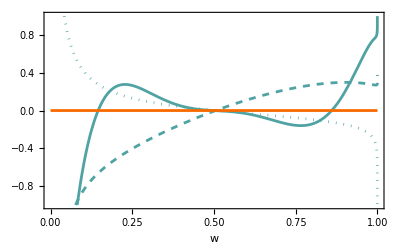

```mathematica
plotσϵσϵ1=Plot[{SSσϵσϵ[w,1/2,2],SSσϵσϵ[w,1/2,5],SSσϵσϵ[w,1/2,8],0},{w,0,1},
PlotStyle->{{colorS,Dotted},{colorS,Dashed},colorS,colorT},
FrameLabel->"w",Frame->True,PlotRange->{{0,1},{-1,1}}]
```

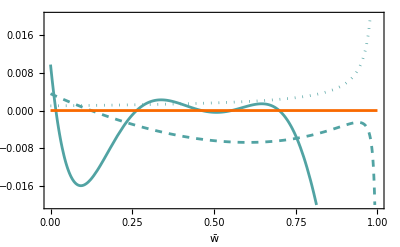

```mathematica
plotσϵσϵ2=Plot[{SSσϵσϵ[1/2,w,2],SSσϵσϵ[1/2,w,5],SSσϵσϵ[1/2,w,8],0},{w,0,1},
PlotStyle->{{colorS,Dotted},{colorS,Dashed},colorS,colorT},
FrameLabel->"w̄",Frame->True,PlotRange->{{0,1},{-0.02,0.02}}]
```

```mathematica
j0=0;
j0bar=2;
```

```mathematica
Sσϵσϵ[h_]=S[hσ,hϵ,hσ,hϵ,h,j0]//FullSimplify
Sϵσϵσ[h_]=S[hϵ,hσ,hϵ,hσ,h,j0bar]//FullSimplify
```

-(16 Cos[(1/16-h) π] Gamma[2 h])/((-9+16 h) π Gamma[7/16+h] Gamma[9/16+h])

Gamma[2 h]/((41/16-h) (25/16+h) Gamma[9/16-h] Gamma[-7/16+h]^3)

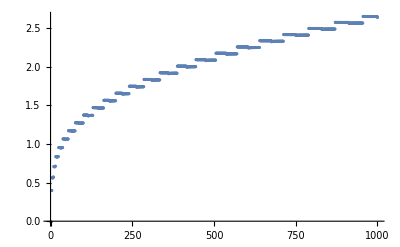

```mathematica
Map[#⟦3⟧Sσϵσϵ[#[[1]]]Sϵσϵσ[#⟦2⟧]&,C2σϵ[[1;;1000]]]//Accumulate//ListPlot
```

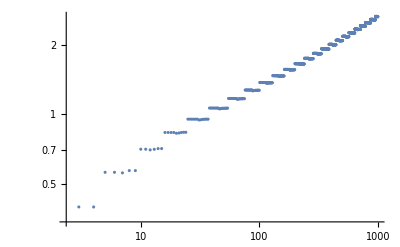

```mathematica
Map[#⟦3⟧Sσϵσϵ[#[[1]]]Sϵσϵσ[#⟦2⟧]&,C2σϵ[[1;;1000]]]//Accumulate//ListLogLogPlot
```

```mathematica
Tσϵσϵ0=T0[hσ,hϵ,j0]
Tϵσϵσ0=T0[hϵ,hσ,j0bar]
Tσϵσϵ[h_]=T[hσ,hϵ,hσ,hϵ,h,j0]//FullSimplify
Tϵσϵσ[h_]=T[hϵ,hσ,hϵ,hσ,h,j0bar]//FullSimplify
```

1

128/(9 Gamma[1/8]^2)

(HypergeometricPFQ[{h,h,h},{2 h,1+h},1] Sin[h π])/(h π)

(Gamma[h] Gamma[2 h] HypergeometricPFQRegularized[{-7/8+h,h,h,h},{-2+h,2 h,17/8+h},1])/Gamma[1/8-h]

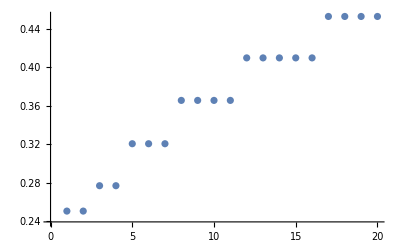

```mathematica
Map[#⟦3⟧If[#⟦1⟧==0,Tσϵσϵ0, Tσϵσϵ[#⟦1⟧]] If[#⟦2⟧==0,Tϵσϵσ0, Tϵσϵσ[#⟦2⟧]]&,CσσCϵϵ[[1;;20]]]//Accumulate//ListPlot
```

#### ⟨σσϵϵ⟩

```mathematica
SSσσϵϵ[w_,wbar_,Λ_]:=Sum[hhc[[3]]S[hσ,hσ,hϵ,hϵ,hhc[[1]]][w]S[hϵ,hϵ,hσ,hσ,hhc[[2]]][wbar],{hhc,cutoff[Λ,CσσCϵϵ]}];
```

```mathematica
TTσσϵϵ[w_,wbar_,Λ_]:=Sum[hhc[[3]]T[hσ,hσ,hϵ,hϵ,hhc[[1]]][w]T[hϵ,hϵ,hσ,hσ,hhc[[2]]][wbar],{hhc,cutoff[Λ,C2σϵ]}];
```

```mathematica
SSσσϵϵ[w,wbar,4]
```

(9 (1-16 w) (1-2 wbar))/(16 w^(7/8) Gamma[1/8])

```mathematica
SSσσϵϵ[w,1/2,16]
```

0

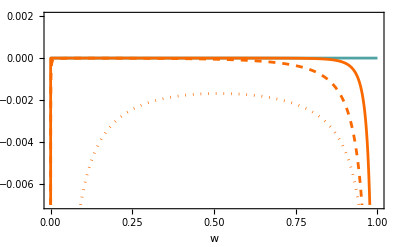

```mathematica
plotσσϵϵ1=Plot[{0,TTσσϵϵ[w,1/2,2],TTσσϵϵ[w,1/2,6],TTσσϵϵ[w,1/2,10]},{w,0,1},
PlotStyle->{colorS,{colorT,Dotted},{colorT,Dashed},colorT},
FrameLabel->"w",Frame->True,PlotRange->{{0,1},{-0.007,0.002}}]
```

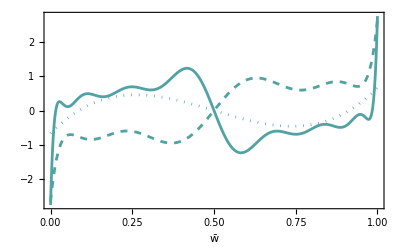

```mathematica
plotσσϵϵ2s=Plot[{SSσσϵϵ[1/2,w,6],SSσσϵϵ[1/2,w,12],SSσσϵϵ[1/2,w,18]},{w,0,1},
PlotStyle->{{colorS,Dotted},{colorS,Dashed},colorS},
FrameLabel->"w̄",Frame->True]
```

Remark: in this case we do not know the sign of the OPE coefficients  in the intersection of σ×σ and ϵ×ϵ
(they are not squares, so they can take either sign), so this plot could be wrong.

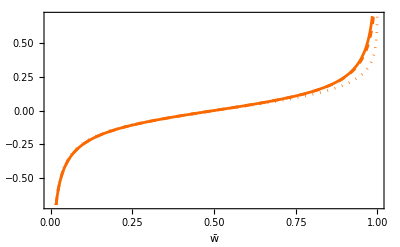

```mathematica
plotσσϵϵ2t=Plot[{TTσσϵϵ[1/2,w,2],TTσσϵϵ[1/2,w,6],TTσσϵϵ[1/2,w,10]},{w,0,1},
PlotStyle->{{colorT,Dotted},{colorT,Dashed},colorT},
FrameLabel->"w̄",Frame->True,PlotRange->{{0,1},{-0.7,0.7}}]
```